```mathematica
ps[d_,s_,t_]:=(-s/(s^2+(1+t)^2))-d Sum[Sin[s Log[d j]](d j)^t,{j,1,1/d}]
ps2[d_,s_,t_]:=(1/d)(-s/(s^2+(1+t)^2))-Sum[Sin[s Log[d j]](d j)^t,{j,1,1/d}]
ps3[d_,s_,t_]:=((-s/(s^2+(1+t)^2))-d Sum[Sin[s Log[d j]](d j)^t,{j,1,1/d}])/(d Sin[s Log[d]]d^t)
ps3a[d_,s_,t_]:=-Sum[j^t Sin[s Log[d j]]/ Sin[s Log[d]],{j,1,Floor[1/d]}]
```

```mathematica
Integrate[Sin[s Log[x]]/x^(1/2),{x,0,1}]
```

ConditionalExpression[-(4 s)/(1+4 s^2),-1/2<Im[s]<1/2]

```mathematica
Integrate[Sin[s Log[x]]/x^(1/3),{x,0,1}]
```

ConditionalExpression[-(9 s)/(4+9 s^2),-2/3<Im[s]<2/3]

```mathematica
Integrate[Sin[s Log[x]] /x^t,{x,0,1}]
```

ConditionalExpression[-s/(s^2+(-1+t)^2),Re[t]<1+Im[s]&&Im[s]+Re[t]<1]

```mathematica
Integrate[Sin[s Log[x]] x^t,{x,0,1}]
```

ConditionalExpression[-s/(s^2+(1+t)^2),Im[s]<1+Re[t]&&1+Im[s]+Re[t]>0]

```mathematica
ps2[.00001,N@Im@ZetaZero@1,-1]
```

-15918.5

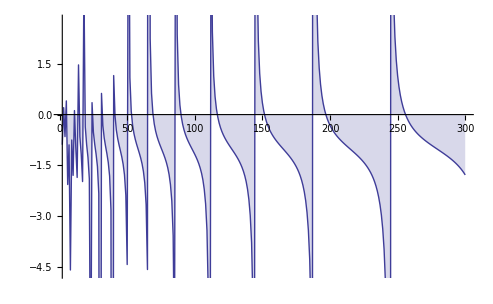

```mathematica
DiscretePlot[Re@ps3[1/d,12.,-.75],{d,2,300}]
```

```mathematica
Integrate[Sin[s Log[x]]/x^(1/2),{x,0,1}]
```

ConditionalExpression[-(4 s)/(1+4 s^2),-1/2<Im[s]<1/2]

```mathematica
Integrate[Tan[s Log[x]]/x^(1/2),{x,0,1}]
```

$Aborted

```mathematica
Integrate[Sin[s Log[x]]/x^(1/2),{x,0,1}]
```

ConditionalExpression[-(4 s)/(1+4 s^2),-1/2<Im[s]<1/2]

```mathematica
Integrate[Sin[s Log[x]+a]/x^k,{x,0,1}]
```

ConditionalExpression[(-s Cos[a]+Sin[a]-k Sin[a])/((-1+k)^2+s^2),Re[k]<1+Im[s]&&Im[s]+Re[k]<1]

```mathematica
FullSimplify[d Sum[Sin[s d t],{t,1,1/d}]]
```

1/2 d (-(-1+Cos[s]) Cot[(d s)/2]+Sin[s])

```mathematica
ex[d_, s_]:=((1-Cos[s])/s)-(1/2 d (-(-1+Cos[s]) Cot[(d s)/2]+Sin[s]))
ex2[d_, s_]:=(1/d)(((1-Cos[s])/s)-(1/2 d (-(-1+Cos[s]) Cot[(d s)/2]+Sin[s])))
```

```mathematica
Limit[ex2[d,s],d->0]
```

-Sin[s]/2

```mathematica
Integrate[Sin[ s Log[x]+ArcTan[2s]]/x^(1/2),{x,0,1}]
```

ConditionalExpression[0,-1/2<Im[s]<1/2]

```mathematica
Integrate[Sin[ s Log[x]+a]x^k,{x,0,1}]
```

ConditionalExpression[(-s Cos[a]+(1+k) Sin[a])/((1+k)^2+s^2),Im[s]<1+Re[k]&&1+Im[s]+Re[k]>0]

```mathematica
FullSimplify[(-s Cos[a]+(1+k) Sin[a])/((1+k)^2+s^2)/.a->ArcTan[2s]/.k->-1/2]
```

0

```mathematica
FullSimplify[(-s Cos[a]+(1+k) Sin[a])/((1+k)^2+s^2)/.k->-1/4/.a->ArcTan[4/3 s]]
```

0

```mathematica
FullSimplify[(-s Cos[a]+(1+k) Sin[a])/((1+k)^2+s^2)/.k->-1/2/.a->ArcTan[2s]]
```

0

```mathematica
FullSimplify[(-s Cos[a]+(1+k) Sin[a])/((1+k)^2+s^2)/.k->-1/3/.a->ArcTan[3/2 s]]
```

0

```mathematica
FullSimplify[(-s Cos[a]+(1+k) Sin[a])/((1+k)^2+s^2)/.k->0/.a->ArcTan[ s]]
```

0

```mathematica
Integrate[Sin[ s Log[x]+ArcTan[s]],{x,0,1}]
```

ConditionalExpression[0,-1<Im[s]<1]

```mathematica
Integrate[Sin[  Log[x^s E^ArcTan[2s]]]/x^(1/2),{x,0,1}]
```

ConditionalExpression[0,-1/2<Im[s]<1/2]

```mathematica
TrigToExp[Sin[Log[x]]]
```

(ⅈ x^-ⅈ)/2-(ⅈ x^ⅈ)/2

```mathematica
2Integrate[Cosh[-(1/2-s)Log[x]]/x^(1/2),{x,0,1}]
```

2/(2 s-2 s^2)

```mathematica
FullSimplify[1/(2 s-2 s^2)]
```

1/(2 s-2 s^2)

```mathematica
Integrate[(2s Cos[s Log[x]]-Sin[ s Log[x]])/x^(1/2)/(2s)^(1/2),{x,0,1}]
```

ConditionalExpression[(4 √2 √s)/(1+4 s^2),s∈Reals]

```mathematica
Integrate[(Cos[s Log[x]]+2s Sin[ s Log[x]])/x^(1/2)/(2s)^(1/2),{x,0,1}]
```

ConditionalExpression[(√2 (1-4 s^2))/(√s (1+4 s^2)),s∈Reals]

```mathematica
Integrate[Sin[s Log[x]]/x^(1/2),{x,0,113}]
```

ConditionalExpression[(2 √113 (-2 s Cos[s Log[113]]+Sin[s Log[113]]))/(1+4 s^2),-1/2<Im[s]<1/2]

```mathematica
ap[n_,s_]:=Sum[Sin[s Log[x]]/x^(1/2),{x,1,n}]-(2 √n (-2 s Cos[s Log[n]]+Sin[s Log[n]]))/(1+4 s^2)
```

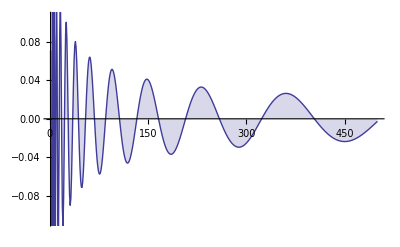

```mathematica
DiscretePlot[ap[n,N@Im@ZetaZero@1],{n,1,500}]
```

```mathematica
Integrate[Sin[s Log[x]+ArcTan[2s]]/x^(1/2),{x,0,113}]
```

ConditionalExpression[(2 √113 Sin[s Log[113]])/(√(1+4 s^2)),-1/2<Im[s]<1/2]

```mathematica
ke[d_,s_]:=2d^(-1/2)Sum[t^(-1/2)Sin[-s Log[d t]-ArcTan[2s]],{t,1,1/d}]
```

```mathematica
ke[1./1000,N@Im@ZetaZero@10]
```

-0.499975

```mathematica
ag[s_]:=DiscretePlot[{-3,Abs@ke[1/n,s],Sin[ArcTan[s]]},{n,1,2000}]
```

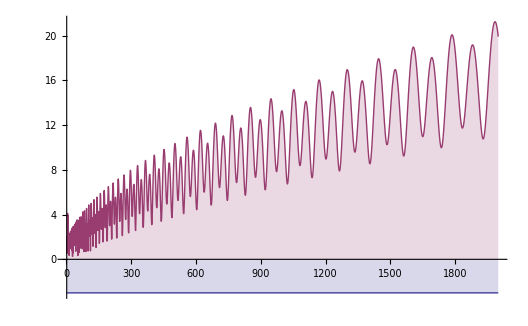

```mathematica
ag[N@Im@ZetaZero@12+3+.1I]
```

```mathematica
ke[.000001,14.]
```

0.0942849

```mathematica
ke[.1,14.]
```

-0.250178

```mathematica
Limit[Sum[t^(-1/2)Sin[-s Log[d t]-ArcTan[2s]],{t,1,1/d}]/.s->10,d->0]
```

Limit[∑_(t=1)^(1/d) -Sin[ArcTan[20]+10 Log[d t]]/(√t),d→0]

```mathematica
Sin[ArcTan[N@Im@ZetaZero@11]]
```

0.999822

```mathematica
ke2a[n_,s_]:=(-1/2-s)n^(1/2-s)(Zeta[1/2-s]-HarmonicNumber[n,1/2-s])-(-1/2+s)n^(1/2+s)(Zeta[1/2+s]-HarmonicNumber[n,1/2+s])
```

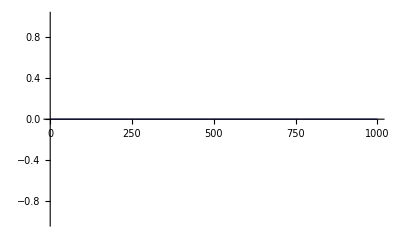

```mathematica
Plot[{Re@ke2a[n,N@Im@ZetaZero@100 I]},{n,1,1000}]
```

```mathematica
Im[-Sinh[ArcTanh[2(N@Im@ZetaZero@1 I+.1)]]]
```

-0.999375

```mathematica
Arg[(1-2s I)]/.s->3+2I
```

-ArcTan[6/5]

```mathematica
E^(I ArcTan[2s])/.s->3+2I
```

0.106846+0.920588 ⅈ

```mathematica
Integrate[ (2s Cos[s Log[x]]+Sin[s Log[x]])/x^(1/2),{x,0,1}]
```

ConditionalExpression[0,s∈Reals]

```mathematica
Integrate[ (Cos[s Log[x]]-2s Sin[s Log[x]])/x^(1/2),{x,0,1}]
```

ConditionalExpression[2,s∈Reals]

```mathematica
Integrate[ ( Sin[s Log[x]+ArcTan[2s]])/x^(1/2),{x,0,1}]
```

ConditionalExpression[0,-1/2<Im[s]<1/2]

```mathematica
Integrate[ ( Sin[s Log[x]-ArcTan[-1/(2s)]])/x^(1/2),{x,0,1}]
```

ConditionalExpression[(2 √(4+1/s^2) s (1-4 s^2))/((1+4 s^2)^2),-1/2<Im[s]<1/2]

```mathematica
ec[n_,s_]:=2Sum[(n/j)^(1/2)Sin[s Log[n/j]-ArcTan[2s]],{j,1,n}]+I(E^(-I ArcTan[2s])n^(1/2+s I)Zeta[1/2+s I]-E^(I ArcTan[2s])n^(1/2-s I)Zeta[1/2-s I])+Sin[ArcTan[2s]]
eca[n_,s_]:={2Sum[(n/j)^(1/2)Sin[s Log[n/j]-ArcTan[2s]],{j,1,n}],I E^(-I ArcTan[2s])n^(1/2+s I)Zeta[1/2+s I],-I E^(I ArcTan[2s])n^(1/2-s I)Zeta[1/2-s I],Sin[ArcTan[2s]]}
eca2[n_,s_]:={2Sum[(n/j)^(1/2)Sin[s Log[n/j]-ArcTan[2s]],{j,1,n}],{I E^(-I ArcTan[2s]),n^(1/2+s I),Zeta[1/2+s I]},{-I E^(I ArcTan[2s]),n^(1/2-s I),Zeta[1/2-s I]},Sin[ArcTan[2s]]}
```

```mathematica
eca[10000,N@Im@ZetaZero@3+2]
```

{233.397,-117.199-228.355 ⅈ,-117.199+228.355 ⅈ,0.999829}

```mathematica
pe[s_,t_]:=(4 Sin[t]-8 s Cos[t])/(1+4s^2)
```

```mathematica
FullSimplify[pe[s,ArcTan[2s]]]
```

0

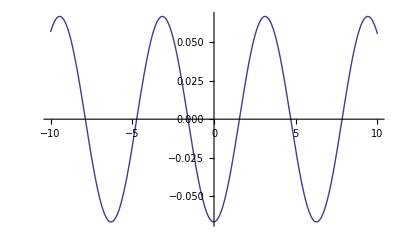

```mathematica
Plot[pe[30,t],{t,-10,10}]
```

```mathematica
N@ArcTan[2 30]
```

1.55413

```mathematica
FullSimplify[I E^(-I s) / (-Sin[s])]
```

-1-ⅈ Cot[s]

```mathematica
FullSimplify[-I E^(I s) / (-Sin[s])]
```

-1+ⅈ Cot[s]

```mathematica
FullSimplify[(4Sin[s]-8s Cos[s])/((1+4s^2)(-Sin[s]))]
```

(-4+8 s Cot[s])/(1+4 s^2)

```mathematica
FullSimplify[Sin[a-theta]/Sin[-theta]]
```

Cos[a]-Cot[theta] Sin[a]

```mathematica
Cot[ArcTan[2s]]
```

1/(2 s)

```mathematica
FullSimplify[(-4+8 s Cot[s])/(1+4 s^2)/.s->ArcTan[2s]]
```

(-4 s+4 ArcTan[2 s])/(s+4 s ArcTan[2 s]^2)

```mathematica
FullSimplify[FullSimplify[Sin[a-ArcTan[2s]]/-Sin[ArcTan[2s]]]/.a->s Log[d t]]
```

Cos[s Log[d t]]-Sin[s Log[d t]]/(2 s)

```mathematica
Integrate[x^(-1/2)(1/(2s)Sin[s Log[x]]+Cos[s Log[x]]),{x,0,1}]
```

ConditionalExpression[0,s∈Reals]

```mathematica
feh[n_,s_]:=Sum[(n/j)^(1/2)Sin[s Log[n/j]-ArcTan[2s]],{j,1,n}]
feh2[n_,s_]:=Sum[(n/j)^(1/2)(Cos[s Log[n/j]]-(1/(2s))Sin[s Log[n/j]]),{j,1,n}]
```

```mathematica
feh2[1000,N@Im@ZetaZero@1]
```

0.5

```mathematica
ecc[n_,s_]:=2Sum[(n/j)^(1/2)Sin[s Log[n/j]-ArcTan[2s]],{j,1,n}]+I(E^(-I ArcTan[2s])n^(1/2+s I)Zeta[1/2+s I]-E^(I ArcTan[2s])n^(1/2-s I)Zeta[1/2-s I])+Sin[ArcTan[2s]]
ecc2[n_,s_]:=2Sum[(n/j)^(1/2)Sin[s Log[n/j]-ArcTan[2s]]/Sin[ArcTan[2s]],{j,1,n}]+I(E^(-I ArcTan[2s])/Sin[ArcTan[2s]]n^(1/2+s I)Zeta[1/2+s I]-E^(I ArcTan[2s])/Sin[ArcTan[2s]]n^(1/2-s I)Zeta[1/2-s I])+Sin[ArcTan[2s]]/Sin[ArcTan[2s]]
ecc3[n_,s_]:=Sum[(n/j)^(1/2)Sin[s Log[n/j]-ArcTan[2s]]/Sin[ArcTan[2s]],{j,1,n}]+I E^(-I ArcTan[2s])/Sin[ArcTan[2s]]/2n^(1/2+s I)Zeta[1/2+s I]- I E^(I ArcTan[2s])/Sin[ArcTan[2s]]/2n^(1/2-s I)Zeta[1/2-s I]+1/2
ecc4[n_,s_]:=Sum[(n/j)^(1/2)Sin[s Log[n/j]-ArcTan[2s]]/Sin[ArcTan[2s]],{j,1,n}]+I E^(-I ArcTan[2s])/Sin[ArcTan[2s]]/2n^(1/2+s I)Zeta[1/2+s I]- I E^(I ArcTan[2s])/Sin[ArcTan[2s]]/2n^(1/2-s I)Zeta[1/2-s I]+1/2
```

```mathematica
ecc4[1000,2.2+1.7I]
```

-4.65661×10^-9-2.44472×10^-9 ⅈ

```mathematica
ecc[1000,2.2+1.7I]
```

-3.60283×10^-9-2.34328×10^-9 ⅈ

```mathematica
Integrate[ Sin[s Log[x]]/(x)^(1/2),{x,0,1}]
```

ConditionalExpression[-(4 s)/(1+4 s^2),-1/2<Im[s]<1/2]

```mathematica
Integrate[Sin[s Log[x]+ArcTan[2s]]/x^(1/2),{x,0,1}]
```

ConditionalExpression[0,-1/2<Im[s]<1/2]

```mathematica
ecx[n_,s_]:=-(-(8 s)/((1+4 s^2)^(3/2)))n+2Sum[(n/j)^(1/2)Sin[s Log[n/j]-(-ArcTan[2s])],{j,1,n}]+I(E^(-I (-ArcTan[2s]))n^(1/2+s I)Zeta[1/2+s I]-E^(I(-ArcTan[2s]))n^(1/2-s I)Zeta[1/2-s I])+Sin[(-ArcTan[2s])]
```

```mathematica
ecx[1000,2.2+1.7I]
```

113.793-365.831 ⅈ

```mathematica
ecr[n_,s_,a_]:=((-8  s Cos[a]+4Sin[a])/(1+4 s^2))n+2Sum[(n/j)^(1/2)Sin[s Log[n/j]-a],{j,1,n}]+I(E^(-I a)n^(1/2+s I)Zeta[1/2+s I]-E^(I a)n^(1/2-s I)Zeta[1/2-s I])+Sin[a]
ecr2[n_,s_,a_]:=((-8  s Cos[a]+4Sin[a])/(1+4 s^2))n-2Sum[(j/n)^(-1/2)Sin[s Log[j/n]+a],{j,1,n}]+I(E^(-I a)n^(1/2+s I)Zeta[1/2+s I]-E^(I a)n^(1/2-s I)Zeta[1/2-s I])+Sin[a]
ecr3[d_,s_,a_]:=((-4  s Cos[a]+2Sin[a])/(1+4 s^2))d^-1-Sum[(d j)^(-1/2)Sin[s Log[d j]+a],{j,1,1/d}]+(1/2)I(E^(-I a)d^(-1/2-s I)Zeta[1/2+s I]-E^(I a)d^(-1/2+s I)Zeta[1/2-s I])+Sin[a]/2
```

```mathematica
ecr3[1/1000.,2.2,ArcTan[2 2.2]]
```

2.77609×10^-11+0. ⅈ

```mathematica
Integrate[Sin[s Log[x]+a]/x^(1/2),{x,0,1}]
```

(2 (-2 s Cos[a]+Sin[a]))/(1+4 s^2)

```mathematica
(2 (-2 s Cos[a]+Sin[a]))/(1+4 s^2)/.a->Pi/2
```

2/(1+4 s^2)

```mathematica
Integrate[x^(s I - 1 /2),{x,0,1}]
```

ConditionalExpression[(2 ⅈ)/(ⅈ-2 s),Im[s]<1/2]

```mathematica
FullSimplify[Cos[s Log[x]]+I Sin[s Log[x]]]
```

x^(ⅈ s)

```mathematica
-2 s / 2 / I
```

ⅈ s

```mathematica
Integrate[x^(s),{x,0,1}]
```

ConditionalExpression[1/(1+s),Re[s]>-1]

```mathematica
Expand[((-1/n^(-1/2+s)-(1/2+s)/2 n^(-1/2+s))-(-1/n^(-1/2-s)-(1/2-s)/2 n^(-1/2-s)))/
(((1/2+s)/2)^(1/2)((1/2-s)/2)^(1/2))]
```

n^(-1/2-s)/(2 √(1/2-s) √(1/2+s))-(2 n^(1/2-s))/(√(1/2-s) √(1/2+s))-n^(-1/2+s)/(2 √(1/2-s) √(1/2+s))+(2 n^(1/2+s))/(√(1/2-s) √(1/2+s))-(n^(-1/2-s) s)/(√(1/2-s) √(1/2+s))-(n^(-1/2+s) s)/(√(1/2-s) √(1/2+s))

```mathematica
FullSimplify[((1/2+s)(1/2-s))^(1/2)]
```

1/2 √(1-4 s^2)

```mathematica
FullSimplify[((1/2+s)/(1/2-s))^(1/2)]
```

√((1+2 s)/(1-2 s))

```mathematica
FullSimplify[E^(-s Log[n])-E^(s Log[n])]
```

n^-s-n^s

```mathematica
TrigToExp[2I Sin[s Log[j]]]
```

-j^(-ⅈ s)+j^(ⅈ s)

```mathematica
Integrate[j^(-1/2+s I),{j,0,n}]
```

ConditionalExpression[(2 ⅈ n^(1/2+ⅈ s))/(ⅈ-2 s),Im[s]<1/2]

```mathematica
TrigToExp[I Sin[s Log[n]]]
```

-1/2 n^(-ⅈ s)+n^(ⅈ s)/2

```mathematica
a1[s_]:=1/(1/2-s I)-1/(1/2+s I)
a2[s_]:=((1/2+s I)^(1/2)(1/2-s I)^(1/2)/(1/2-s I)-(1/2+s I)^(1/2)(1/2-s I)^(1/2)/(1/2+s I))/(1/2-s I)^(1/2)/(1/2+s I)^(1/2)
a3[s_]:=((1/2+s I)^(1/2)(1/2-s I)^(1/2)/(1/2-s I)-(1/2+s I)^(1/2)(1/2-s I)^(1/2)/(1/2+s I))/(1/2-s I)^(1/2)/(1/2+s I)^(1/2)
```

```mathematica
a3[.3+2I]
a1[.3+2I]
```

1.03535+0.175524 ⅈ

1.03535+0.175524 ⅈ

```mathematica
FullSimplify[(1/2+s I)^(1/2)(1/2-s I)^(1/2)/(1/2-s I)]
```

(√(1+2 ⅈ s))/(√(1-2 ⅈ s))

```mathematica
FullSimplify[((1/2+s I)^(1/2)(1/2-s I)^(1/2)/(1/2+s I))]
```

(√(1-2 ⅈ s))/(√(1+2 ⅈ s))

```mathematica
FullSimplify[1/(1/2-s I)^(1/2)/(1/2+s I)^(1/2)]
```

2/(√(1+4 s^2))

```mathematica
FullSimplify@Log[(√(1+2 ⅈ s))/(√(1-2 ⅈ s))]
```

ⅈ ArcTan[2 s]

```mathematica
FullSimplify@Log[(√(1-2 ⅈ s))/(√(1+2 ⅈ s))]
```

-ⅈ ArcTan[2 s]

```mathematica
2Cos[ArcTan[2s]]
```

2/(√(1+4 s^2))

```mathematica
b1[n_,s_]:=n^(1/2-s I)/(1/2+s I)-n^(1/2+s I)/(1/2-s I)
b2[n_,s_]:=n^(1/2)(n^(-s I)/(1/2+s I)-n^(s I)/(1/2-s I))
b3[n_,s_]:=n^(1/2)((1/2-s I)^(1/2)(1/2+s I)^(1/2)n^(-s I)/(1/2+s I)-(1/2-s I)^(1/2)(1/2+s I)^(1/2)n^(s I)/(1/2-s I))/(1/2-s I)^(1/2)/(1/2+s I)^(1/2)
b4[n_,s_]:=2Cos[ArcTan[2s]]n^(1/2)((1/2-s I)^(1/2)(1/2+s I)^(1/2)n^(-s I)/(1/2+s I)-(1/2-s I)^(1/2)(1/2+s I)^(1/2)n^(s I)/(1/2-s I))
b5[n_,s_]:=2Cos[ArcTan[2s]]n^(1/2)((1/2-s I)^(1/2)(1/2+s I)^(1/2)/(1/2+s I)n^(-s I)-(1/2-s I)^(1/2)(1/2+s I)^(1/2)/(1/2-s I)n^(s I))
b6[n_,s_]:=2Cos[ArcTan[2s]]n^(1/2)(E^(-ⅈ ArcTan[2 s])n^(-s I)-E^(ⅈ ArcTan[2 s])n^(s I))
b7[n_,s_]:=2Cos[ArcTan[2s]]n^(1/2)(E^(-ⅈ ArcTan[2 s])E^(-s Log[n] I)-E^(ⅈ ArcTan[2 s])E^(s Log[n] I))
b8[n_,s_]:=2Cos[ArcTan[2s]]n^(1/2)(E^(-ⅈ ArcTan[2 s] + -s Log[n] I)-E^(s Log[n] I + ⅈ ArcTan[2 s]))
b10[n_,s_]:=-4 ⅈ Cos[ArcTan[2s]]n^(1/2)Sin[s Log[n]+ArcTan[2 s]]
```

```mathematica
b10[100,.3+1.2I]
```

-1846.35+2733.03 ⅈ

```mathematica
b1[100,.3+1.2I]
```

-1846.35+2733.03 ⅈ

```mathematica
FullSimplify[1/(1/2-s I)^(1/2)/(1/2+s I)^(1/2)]
```

2/(√(1+4 s^2))

```mathematica
FullSimplify@Log[(1/2-s I)^(1/2)(1/2+s I)^(1/2)/(1/2+s I)]
```

-ⅈ ArcTan[2 s]

```mathematica
FullSimplify@Log[(1/2-s I)^(1/2)(1/2+s I)^(1/2)/(1/2-s I)]
```

ⅈ ArcTan[2 s]

```mathematica
ExpToTrig[(E^(-ⅈ (ArcTan[2 s] + s Log[n]) )-E^(I ( s Log[n]  + ArcTan[2 s] )))]
```

-2 ⅈ Sin[ArcTan[2 s]+s Log[n]]

```mathematica
c1[n_,s_]:=n^(1/2-s I)/(1/2+s I)+n^(1/2+s I)/(1/2-s I)
c8[n_,s_]:=2Cos[ArcTan[2s]]n^(1/2)(E^(-ⅈ ArcTan[2 s] + -s Log[n] I)+E^(s Log[n] I + ⅈ ArcTan[2 s]))
c10[n_,s_]:=4 Cos[ArcTan[2s]]n^(1/2)Cos[s Log[n]+ArcTan[2 s]]
```

```mathematica
c10[100,.3+.2I]
```

-34.3604-43.8865 ⅈ

```mathematica
c1[100,.3+.2I]
```

-34.3604-43.8865 ⅈ

```mathematica
Integrate[Cos[13 Log[j]]/j^(1/2),{j,0,n}]
```

2/677 √n (Cos[13 Log[n]]+26 Sin[13 Log[n]])

```mathematica
Integrate[Sin[13 Log[j]]/j^(1/2),{j,0,n}]
```

-2/677 √n (26 Cos[13 Log[n]]-Sin[13 Log[n]])

```mathematica
cal0[n_,s_]:=Sum[j^(-1/2+s I),{j,1,n}]-1/2 n^(-1/2+ⅈ s)-n^(1/2+ⅈ s)/(1/2+ⅈ s)
z1[s_]:=Zeta[1/2+s I]
cal01[n_,s_]:=Sum[j^(-1/2-s I),{j,1,n}]-1/2 n^(-1/2-ⅈ s)-n^(1/2-ⅈ s)/(1/2-ⅈ s)
z1i[s_]:=Zeta[1/2-s I]
calx[n_,s_]:=(cal0[n,s]-cal01[n,s])/(2 I)
cal1[n_,s_]:=Sum[Sin[s Log[j]]/j^(1/2),{j,1,n}]+2n^(1/2) Cos[ArcTan[2s]]Sin[s Log[n]+ArcTan[2s]]-Sin[s Log[n]]/(2 n^(1/2))
rcal[s_]:=1/(2 I)(Zeta[1/2-s I]-Zeta[1/2+s I])
calx2[n_,s_]:=((Sum[j^(-1/2+s I),{j,1,n}]-1/2 n^(-1/2+ⅈ s)-n^(1/2+ⅈ s)/(1/2+ⅈ s))-(Sum[j^(-1/2-s I),{j,1,n}]-1/2 n^(-1/2-ⅈ s)-n^(1/2-ⅈ s)/(1/2-ⅈ s)))/(2 I)
calx3[n_,s_]:=((Sum[j^(-1/2+s I)-j^(-1/2-s I),{j,1,n}]-(1/2 n^(-1/2+ⅈ s)-1/2 n^(-1/2-ⅈ s))-(n^(1/2+ⅈ s)/(1/2+ⅈ s)-n^(1/2-ⅈ s)/(1/2-ⅈ s))))/(2 I)
calx4[n_,s_]:=((Sum[j^(-1/2)(j^(s I)-j^(-s I)),{j,1,n}]-(1/2 n^(-1/2)(n^(ⅈ s)-n^(-ⅈ s)))-n^(1/2)(n^(ⅈ s)/(1/2+ⅈ s)-n^(-ⅈ s)/(1/2-ⅈ s))))/(2 I)
calx5[n_,s_]:=((2 I Sum[j^(-1/2)Sin[s Log[j]],{j,1,n}]-(1/2 n^(-1/2)(n^(ⅈ s)-n^(-ⅈ s)))-n^(1/2)(n^(ⅈ s)/(1/2+ⅈ s)-n^(-ⅈ s)/(1/2-ⅈ s))))/(2 I)
calx6[n_,s_]:=((2 I Sum[j^(-1/2)Sin[s Log[j]],{j,1,n}]-(I n^(-1/2)Sin[s Log[n]])-n^(1/2)(n^(ⅈ s)/(1/2+ⅈ s)-n^(-ⅈ s)/(1/2-ⅈ s))))/(2 I)
calx7[n_,s_]:=((2 I Sum[j^(-1/2)Sin[s Log[j]],{j,1,n}]-(I n^(-1/2)Sin[s Log[n]])-n^(1/2)/(1/2+I s)^(1/2)/(1/2-I s)^(1/2)((n^(ⅈ s)(1/2+I s)^(1/2)(1/2-I s)^(1/2))/(1/2+ⅈ s)-(n^(-ⅈ s)(1/2+I s)^(1/2)(1/2-I s)^(1/2))/(1/2-ⅈ s))))/(2 I)
calx8[n_,s_]:=((2 I Sum[j^(-1/2)Sin[s Log[j]],{j,1,n}]-(I n^(-1/2)Sin[s Log[n]])-n^(1/2)/(1/2+I s)^(1/2)/(1/2-I s)^(1/2)((n^(ⅈ s)(1/2-I s)^(1/2))/(1/2+ⅈ s)^(1/2)-(n^(-ⅈ s)(1/2+I s)^(1/2))/(1/2-ⅈ s)^(1/2))))/(2 I)
calx9[n_,s_]:=((2 I Sum[j^(-1/2)Sin[s Log[j]],{j,1,n}]-(I n^(-1/2)Sin[s Log[n]])-n^(1/2)2Cos[ArcTan[2s]]((n^(ⅈ s)(1/2-I s)^(1/2))/(1/2+ⅈ s)^(1/2)-(n^(-ⅈ s)(1/2+I s)^(1/2))/(1/2-ⅈ s)^(1/2))))/(2 I)
calx10[n_,s_]:=((2 I Sum[j^(-1/2)Sin[s Log[j]],{j,1,n}]-(I n^(-1/2)Sin[s Log[n]])-n^(1/2)2Cos[ArcTan[2s]](E^(-ⅈ ArcTan[2 s])n^(ⅈ s)-E^(ⅈ ArcTan[2 s])n^(-ⅈ s))))/(2 I)
calx11[n_,s_]:=((2 I Sum[j^(-1/2)Sin[s Log[j]],{j,1,n}]-(I n^(-1/2)Sin[s Log[n]])-n^(1/2)2Cos[ArcTan[2s]](E^(-ⅈ ArcTan[2 s])E^(ⅈ s Log[n])-E^(ⅈ ArcTan[2 s])E^(-ⅈ s Log[n]))))/(2 I)
calx12[n_,s_]:=((2 I Sum[j^(-1/2)Sin[s Log[j]],{j,1,n}]-(I n^(-1/2)Sin[s Log[n]])-n^(1/2)2Cos[ArcTan[2s]](E^(ⅈ s Log[n]-ⅈ ArcTan[2 s])-E^(-ⅈ s Log[n]+ⅈ ArcTan[2 s]))))/(2 I)
calx13[n_,s_]:= Sum[j^(-1/2)Sin[s Log[j]],{j,1,n}]-n^(1/2)Cos[ArcTan[2s]]2 Sin[s Log[n]-ArcTan[2s]]- n^(-1/2)/2 Sin[s Log[n]]
rcala[s_]:=1/(2 I)(Zeta[1/2-s I]-Zeta[1/2+s I])
```

```mathematica
calx13[10000,12.+.1I]
```

0.746892+0.0120629 ⅈ

```mathematica
rcala[12.+.1I]
```

0.746893+0.0120623 ⅈ

```mathematica
calx[10000,2.+.1I]
```

0.310829-0.029081 ⅈ

```mathematica
FullSimplify[1/(1/2+I s)^(1/2)/(1/2-I s)^(1/2)]
```

2/(√(1+4 s^2))

```mathematica
FullSimplify[Log[(1/2-I s)^(1/2)/(1/2+ⅈ s)^(1/2)]]
```

-ⅈ ArcTan[2 s]

```mathematica
FullSimplify[Log[(1/2+I s)^(1/2)/(1/2-ⅈ s)^(1/2)]]
```

ⅈ ArcTan[2 s]

```mathematica
balx13[n_,s_]:= Sum[j^(-1/2)Cos[s Log[j]],{j,1,n}]-n^(1/2)Cos[ArcTan[2s]]2 Cos[s Log[n]-ArcTan[2s]]- n^(-1/2)/2 Cos[s Log[n]]
rcalb[s_]:=1/(2 )(Zeta[1/2-s I]+Zeta[1/2+s I])
```

```mathematica
balx13[10000,12.+.1I]
rcalb[12.+.1I]
```

1.01688-0.0525293 ⅈ

1.01688-0.0525302 ⅈ

```mathematica
Limit[Cos[(300+.5I) Log[n]]/n^(1/2),n->Infinity]
```

0.5 2.71828^((0.+2. ⅈ) Interval[{-8.9003×10^-308,3.14159}])

```mathematica
arcal[s_,a_]:=E^(a I)Zeta[1/2-s I]+E^(-a I)Zeta[1/2+s I]
acalx2[n_,s_,a_]:=E^(a I)(Sum[j^(-1/2+s I),{j,1,n}]-1/2 n^(-1/2+ⅈ s)-n^(1/2+ⅈ s)/(1/2+ⅈ s))+E^(-a I)(Sum[j^(-1/2-s I),{j,1,n}]-1/2 n^(-1/2-ⅈ s)-n^(1/2-ⅈ s)/(1/2-ⅈ s))
acalx3[n_,s_,a_]:=Sum[E^(a I)j^(-1/2+s I),{j,1,n}]-1/2 E^(a I)n^(-1/2+ⅈ s)-E^(a I)n^(1/2+ⅈ s)/(1/2+ⅈ s)+Sum[E^(-a I)j^(-1/2-s I),{j,1,n}]-1/2 E^(-a I) n^(-1/2-ⅈ s)-E^(-a I)n^(1/2-ⅈ s)/(1/2-ⅈ s)
acalx4[n_,s_,a_]:=Sum[E^(a I)j^(-1/2+s I)+E^(-a I)j^(-1/2-s I),{j,1,n}]-1/2 E^(a I)n^(-1/2+ⅈ s)-1/2 E^(-a I) n^(-1/2-ⅈ s)-E^(a I)n^(1/2+ⅈ s)/(1/2+ⅈ s)-E^(-a I)n^(1/2-ⅈ s)/(1/2-ⅈ s)
acalx5[n_,s_,a_]:=Sum[j^(-1/2)(E^(a I)E^(s Log[j] I)+E^(-a I)E^(-s Log[j] I)),{j,1,n}]-1/2 n^(-1/2)(E^(a I)n^(ⅈ s)+E^(-a I) n^(-ⅈ s))-E^(a I)n^(1/2+ⅈ s)/(1/2+ⅈ s)-E^(-a I)n^(1/2-ⅈ s)/(1/2-ⅈ s)
acalx6[n_,s_,a_]:=Sum[j^(-1/2)(E^(s Log[j] I+a I)+E^(-s Log[j] I-a I)),{j,1,n}]-1/2 n^(-1/2)(E^(ⅈ s Log[n]+a I)+E^(-ⅈ s Log[n]-a I))-n^(1/2)(E^(ⅈ s Log[n]+a I)/(1/2+ⅈ s)+E^(-ⅈ s Log[n]-a I)/(1/2-ⅈ s))
acalx7[n_,s_,a_]:=2Sum[j^(-1/2)Cos[s Log[j]+a],{j,1,n}]-1/2 n^(-1/2)(E^(ⅈ s Log[n]+a I)+E^(-ⅈ s Log[n]-a I))-n^(1/2)(E^(ⅈ s Log[n]+a I)/(1/2+ⅈ s)+E^(-ⅈ s Log[n]-a I)/(1/2-ⅈ s))
acalx8[n_,s_,a_]:=2Sum[j^(-1/2)Cos[s Log[j]+a],{j,1,n}]- n^(-1/2)Cos[s Log[n]+a]-n^(1/2)(E^(ⅈ s Log[n]+a I)/(1/2+ⅈ s)+E^(-ⅈ s Log[n]-a I)/(1/2-ⅈ s))
acalx9[n_,s_,a_]:=2Sum[j^(-1/2)Cos[s Log[j]+a],{j,1,n}]- n^(-1/2)Cos[s Log[n]+a]-n^(1/2)/(1/2+I s)^(1/2)/(1/2-I s)^(1/2)(((1/2+I s)^(1/2)(1/2-I s)^(1/2)E^(ⅈ s Log[n]+a I))/(1/2+ⅈ s)+((1/2+I s)^(1/2)(1/2-I s)^(1/2)E^(-ⅈ s Log[n]-a I))/(1/2-ⅈ s))
acalx10[n_,s_,a_]:=2Sum[j^(-1/2)Cos[s Log[j]+a],{j,1,n}]- n^(-1/2)Cos[s Log[n]+a]-n^(1/2)2Cos[ArcTan[2s]](E^(-ⅈ ArcTan[2 s])E^(ⅈ s Log[n]+a I)+E^(ⅈ ArcTan[2 s])E^(-ⅈ s Log[n]-a I))
acalx11[n_,s_,a_]:=2Sum[j^(-1/2)Cos[s Log[j]+a],{j,1,n}]- n^(-1/2)Cos[s Log[n]+a]-n^(1/2)2Cos[ArcTan[2s]](E^(ⅈ s Log[n]+a I-ⅈ ArcTan[2 s])+E^(-ⅈ s Log[n]-a I+ⅈ ArcTan[2 s]))
acalx12[n_,s_,a_]:=2Sum[j^(-1/2)Cos[s Log[j]+a],{j,1,n}]- n^(-1/2)Cos[s Log[n]+a]-4 n^(1/2)Cos[ArcTan[2s]]Cos[s Log[n]+a-ArcTan[2s]]
arcal2[s_,a_]:=E^(a I)Zeta[1/2-s I]+E^(-a I)Zeta[1/2+s I]
```

```mathematica
acalx12[10000,12.+.1I,.3]
arcal2[12.+.1I,.3]
```

1.50149-0.107496 ⅈ

1.50149-0.107497 ⅈ

```mathematica
(1/2+I s)^(1/2)(1/2-I s)^(1/2)
```

```mathematica
ExpToTrig[E^(a I)Zeta[1/2-s I]+E^(-a I)Zeta[1/2+s I]]
```

Cos[a] Zeta[1/2-ⅈ s]+ⅈ Sin[a] Zeta[1/2-ⅈ s]+Cos[a] Zeta[1/2+ⅈ s]-ⅈ Sin[a] Zeta[1/2+ⅈ s]

```mathematica
Cos[ArcTan[2s]]
```

1/(√(1+4 s^2))

```mathematica
dcalx12[n_,s_,a_]:=2Sum[j^(-1/2)Cos[s Log[j]+a],{j,1,n}]- n^(-1/2)Cos[s Log[n]+a]-4 n^(1/2)Cos[ArcTan[2s]]Cos[s Log[n]+a-ArcTan[2s]]
dcalx13[n_,s_]:=2Sum[j^(-1/2)Cos[s Log[j]+ArcTan[2s]],{j,1,n}]- n^(-1/2)Cos[s Log[n]+ArcTan[2s]]-4 n^(1/2)Cos[ArcTan[2s]]Cos[s Log[n]+ArcTan[2s]-ArcTan[2s]]
drcal2[s_,a_]:=Cos[a](Zeta[1/2-s I]+Zeta[1/2+s I])+I Sin[a](Zeta[1/2-s I]-Zeta[1/2+s I])
drcal3[s_]:=Cos[ArcTan[2s]](Zeta[1/2-s I]+Zeta[1/2+s I])+I Sin[ArcTan[2s]](Zeta[1/2-s I]-Zeta[1/2+s I])
drcal4[s_]:=1/(√(1+4 s^2))(Zeta[1/2-s I]+Zeta[1/2+s I])+I ((2 s)/(√(1+4 s^2)))(Zeta[1/2-s I]-Zeta[1/2+s I])
dcalx14[n_,s_]:=2Sum[j^(-1/2)Cos[s Log[j]+ArcTan[2s]],{j,1,n}]-n^(-1/2)Cos[s Log[n]+ArcTan[2s]]-4 n^(1/2)1/(√(1+4 s^2))Cos[s Log[n]]
drcal5[s_]:=((Zeta[1/2-s I]+Zeta[1/2+s I])+I (2 s)(Zeta[1/2-s I]-Zeta[1/2+s I]))/2
dcalx15[n_,s_]:=√(1+4 s^2)Sum[j^(-1/2)Cos[s Log[j]+ArcTan[2s]],{j,1,n}]-n^(-1/2)√(1+4 s^2)/2 Cos[s Log[n]+ArcTan[2s]]-2 n^(1/2)Cos[s Log[n]]
```

```mathematica
dcalx15[10000,12.+.1I]
drcal5[12.+.1I]
```

-16.9061-0.491417 ⅈ

-16.9061-0.491403 ⅈ

```mathematica
Cos[ArcTan[2s]]
```

1/(√(1+4 s^2))

```mathematica
FullSimplify[TrigToExp[Cos[s Log[j]+ArcTan[2s]]]]
```

(j^(-ⅈ s) (1+j^(2 ⅈ s) (1+2 ⅈ s)-2 ⅈ s))/(2 √(1+4 s^2))

```mathematica
Cos[ArcTan[2s]-s Log[n]+Pi/2]
```

-Sin[ArcTan[2 s]-s Log[n]]

```mathematica
ecalx12[n_,s_,a_]:=2Sum[j^(-1/2)Cos[s Log[j]+a],{j,1,n}]- n^(-1/2)Cos[s Log[n]+a]-4 n^(1/2)Cos[ArcTan[2s]]Cos[s Log[n]+a-ArcTan[2s]]
ercal2[s_,a_]:=Cos[a](Zeta[1/2-s I]+Zeta[1/2+s I])+I Sin[a](Zeta[1/2-s I]-Zeta[1/2+s I])
ts1[n_,s_]:=ecalx12[n,s,ArcTan[2s]-Pi/2-s Log[n]]
ts2[n_,s_]:=ercal2[s,ArcTan[2s]-Pi/2-s Log[n]]
```

```mathematica
ts1[10000,13.+.1I]
ts2[10000,13.+.1I]
```

1.93821+0.7392 ⅈ

1.93821+0.7392 ⅈ

```mathematica
2Sum[j^(-1/2)Cos[s Log[j]+a],{j,1,n}]- n^(-1/2)Cos[s Log[n]+a]-4 n^(1/2)Cos[ArcTan[2s]]Cos[s Log[n]+a-ArcTan[2s]]/.a->ArcTan[2s]-Pi/2-s Log[n]
```

-(2 s)/(√n √(1+4 s^2))+2 ∑_(j=1)^n Sin[ArcTan[2 s]+s Log[j]-s Log[n]]/(√j)

```mathematica
FullSimplify[Cos[a](Zeta[1/2-s I]+Zeta[1/2+s I])+I Sin[a](Zeta[1/2-s I]-Zeta[1/2+s I])/.a->ArcTan[2s]-Pi/2-s Log[n]]
```

(n^(-ⅈ s) ((-ⅈ+2 s) Zeta[1/2-ⅈ s]+n^(2 ⅈ s) (ⅈ+2 s) Zeta[1/2+ⅈ s]))/(√(1+4 s^2))

```mathematica
Chop[N@Sin[2I+111.1]^2+Cos[2I+111.1]^2]
```

1.

```mathematica
Limit[(2 s)/(√n √(1+4 s^2)),n->Infinity]
```

0

```mathematica
Cos[Pi/2]
```

0

```mathematica
2Sum[j^(-1/2)Cos[s Log[j]+a],{j,1,n}]/.a->ArcTan[2s]-Pi/2-s Log[n]
```

2 ∑_(j=1)^n Sin[ArcTan[2 s]+s Log[j]-s Log[n]]/(√j)

```mathematica
- n^(-1/2)Cos[s Log[n]+a]/.a->ArcTan[2s]-Pi/2-s Log[n]
```

-(2 s)/(√n √(1+4 s^2))

```mathematica
-4 n^(1/2)Cos[ArcTan[2s]]Cos[s Log[n]+a-ArcTan[2s]]/.a->ArcTan[2s]-Pi/2-s Log[n]
```

0

```mathematica
FullSimplify[Cos[a](Zeta[1/2-s I]+Zeta[1/2+s I])/.a->ArcTan[2s]-Pi/2-s Log[n]]
```

Sin[ArcTan[2 s]-s Log[n]] (Zeta[1/2-ⅈ s]+Zeta[1/2+ⅈ s])

```mathematica
I Sin[a](Zeta[1/2-s I]-Zeta[1/2+s I])/.a->ArcTan[2s]-Pi/2-s Log[n]
```

-ⅈ Cos[ArcTan[2 s]-s Log[n]] (Zeta[1/2-ⅈ s]-Zeta[1/2+ⅈ s])

```mathematica
FullSimplify@Expand[Sin[ArcTan[2 s]-s Log[n]] (Zeta[1/2-ⅈ s]+Zeta[1/2+ⅈ s])]
```

Sin[ArcTan[2 s]-s Log[n]] (Zeta[1/2-ⅈ s]+Zeta[1/2+ⅈ s])

```mathematica
FullSimplify[Sin[ArcTan[2 s]-s Log[n]]]
```

Sin[ArcTan[2 s]-s Log[n]]

```mathematica
Cos[a](Zeta[1/2-s I]+Zeta[1/2+s I])+I Sin[a](Zeta[1/2-s I]-Zeta[1/2+s I])/.a->ArcTan[2s]-Pi/2-s Log[n]/.n->100./.s->44.
```

-2.79703+0. ⅈ

-ⅈ Cos[4.60517 s-ArcTan[2 s]] (Zeta[1/2-ⅈ s]-Zeta[1/2+ⅈ s])-Sin[4.60517 s-ArcTan[2 s]] (Zeta[1/2-ⅈ s]+Zeta[1/2+ⅈ s])

```mathematica
TrigToExp[Cos[a](Zeta[1/2-s I]+Zeta[1/2+s I])+I Sin[a](Zeta[1/2-s I]-Zeta[1/2+s I])/.a->ArcTan[2s]-Pi/2-s Log[n]]
```

-ⅈ ⅇ^(1/2 (-Log[1-2 ⅈ s]+Log[1+2 ⅈ s])) n^(-ⅈ s) Zeta[1/2-ⅈ s]+ⅈ ⅇ^(1/2 (Log[1-2 ⅈ s]-Log[1+2 ⅈ s])) n^(ⅈ s) Zeta[1/2+ⅈ s]

```mathematica
FullSimplify[ⅇ^(1/2 (Log[1-2 ⅈ s]-Log[1+2 ⅈ s]))]
```

(√(1-2 ⅈ s))/(√(1+2 ⅈ s))

```mathematica
-ⅈ ⅇ^(1/2 (-Log[1-2 ⅈ s]+Log[1+2 ⅈ s])) n^(-ⅈ s) Zeta[1/2-ⅈ s]+ⅈ ⅇ^(1/2 (Log[1-2 ⅈ s]-Log[1+2 ⅈ s])) n^(ⅈ s) Zeta[1/2+ⅈ s]/.s->44./.n->100.
```

-2.79703+0. ⅈ

```mathematica
FullSimplify[ ⅇ^(1/2 (-Log[1-2 ⅈ s]+Log[1+2 ⅈ s])) ]
```

(√(1+2 ⅈ s))/(√(1-2 ⅈ s))

```mathematica
-ⅈ (√(1+2 ⅈ s))/(√(1-2 ⅈ s)) n^(-ⅈ s) Zeta[1/2-ⅈ s]+ⅈ (√(1-2 ⅈ s))/(√(1+2 ⅈ s)) n^(ⅈ s) Zeta[1/2+ⅈ s]/.s->44./.n->100.
```

-2.79703+8.67362×10^-19 ⅈ

```mathematica
-ⅈ (√(1/2+ ⅈ s))/(√(1/2- ⅈ s)) n^(-ⅈ s) Zeta[1/2-ⅈ s]+ⅈ (√(1/2- ⅈ s))/(√(1/2+ⅈ s)) n^(ⅈ s) Zeta[1/2+ⅈ s]/.s->44./.n->100.
```

-2.79703+2.21177×10^-16 ⅈ

```mathematica
FullSimplify[Cos[a](Zeta[1/2-s I]+Zeta[1/2+s I])/.a->ArcTan[2s]]
```

(Zeta[1/2-ⅈ s]+Zeta[1/2+ⅈ s])/(√(1+4 s^2))

```mathematica
(Zeta[1/2-ⅈ s]+Zeta[1/2+ⅈ s])/(√(1+4 s^2))/.s->3/2I
```

-(ⅈ (-1/12+π^2/6))/(2 √2)

```mathematica
Cos[ArcTan[2s]]
```

1/(√(1+4 s^2))

```mathematica
2Sum[j^(-1/2)Cos[s Log[j]+a],{j,1,n}]- n^(-1/2)Cos[s Log[n]+a]-4 n^(1/2)Cos[ArcTan[2s]]Cos[s Log[n]+a-ArcTan[2s]]/.a->-s Log[n]+ArcTan[2s]+Pi/2
```

(2 s)/(√n √(1+4 s^2))+2 ∑_(j=1)^n -Sin[ArcTan[2 s]+s Log[j]-s Log[n]]/(√j)

```mathematica
scal0[n_,s_]:=(1/2+I s)Sum[j^(-1/2+s I),{j,1,n}]-1/2(1/2+I s) n^(-1/2+ⅈ s)-n^(1/2+ⅈ s)
sz1[s_]:=(1/2+I s)Zeta[1/2-s I]
scal01[n_,s_]:=(1/2-I s)Sum[j^(-1/2-s I),{j,1,n}]-1/2 (1/2-I s)n^(-1/2-ⅈ s)-n^(1/2-ⅈ s)
sz1i[s_]:=(1/2-I s)Zeta[1/2+s I]
sba[n_,s_,a_]:=E^(I a)((1/2+I s)Sum[j^(-1/2+s I),{j,1,n}]-1/2(1/2+I s) n^(-1/2+ⅈ s)-n^(1/2+ⅈ s))+E^(-I a)((1/2-I s)Sum[j^(-1/2-s I),{j,1,n}]-1/2 (1/2-I s)n^(-1/2-ⅈ s)-n^(1/2-ⅈ s))
sra[s_,a_]:=E^(I a)((1/2+I s)Zeta[1/2-s I])+E^(-I a)((1/2-I s)Zeta[1/2+s I])
sba2[n_,s_,a_]:=Sum[E^(I a)(1/2+I s)j^(-1/2+s I)+(1/2-I s)E^(-I a) j^(-1/2-s I),{j,1,n}]-1/2(1/2+I s)E^(I a) n^(-1/2+ⅈ s)-E^(I a)n^(1/2+ⅈ s)-1/2 (1/2-I s)E^(-I a)n^(-1/2-ⅈ s)-E^(-I a)n^(1/2-ⅈ s)
sba3[n_,s_,a_]:=Sum[E^(I a)(1/2+I s)j^(-1/2+s I)+(1/2-I s)E^(-I a) j^(-1/2-s I),{j,1,n}]-1/2(1/2+I s)E^(I a) n^(-1/2+ⅈ s)-1/2 (1/2-I s)E^(-I a)n^(-1/2-ⅈ s)-E^(I a)n^(1/2+ⅈ s)-E^(-I a)n^(1/2-ⅈ s)
sba4[n_,s_,a_]:=Sum[j^(-1/2)(E^(I a)(1/2+I s)j^(s I)+(1/2-I s)E^(-I a) j^(-s I)),{j,1,n}]-1/2 n^(-1/2)((1/2+I s)E^(I a) n^(ⅈ s)+ (1/2-I s)E^(-I a)n^(-ⅈ s))-n^(1/2)(E^(I a)n^(ⅈ s)+E^(-I a)n^(-ⅈ s))
sba5[n_,s_,a_]:=Sum[j^(-1/2)(E^(I a)(1/2+I s)j^(s I)+(1/2-I s)E^(-I a) j^(-s I)),{j,1,n}]-1/2 n^(-1/2)((1/2+I s)E^(I a) n^(ⅈ s)+ (1/2-I s)E^(-I a)n^(-ⅈ s))-n^(1/2)(E^(I a)E^(ⅈ s Log[n])+E^(-I a)E^(-ⅈ s Log[n]))
sba6[n_,s_,a_]:=Sum[j^(-1/2)(E^(I a)(1/2+I s)j^(s I)+(1/2-I s)E^(-I a) j^(-s I)),{j,1,n}]-1/2 n^(-1/2)((1/2+I s)E^(I a) n^(ⅈ s)+ (1/2-I s)E^(-I a)n^(-ⅈ s))-n^(1/2)2Cos[s Log[n]+a]
sba7[n_,s_,a_]:=Sum[j^(-1/2)((1/2+I s)E^(s I Log[j]+I a)+(1/2-I s)E^(-s I Log[j]-I a)),{j,1,n}]-1/2 n^(-1/2)((1/2+I s) E^(ⅈ s Log[n]+a I)+ (1/2-I s)E^(-ⅈ s Log[n]-I a))-n^(1/2)2Cos[s Log[n]+a]
sba8[n_,s_,a_]:=(1/2+I s)^(1/2)(1/2-I s)^(1/2)Sum[j^(-1/2)((1/2+I s)/(1/2+I s)^(1/2)/(1/2-I s)^(1/2)E^(s I Log[j]+I a)+(1/2-I s)/(1/2+I s)^(1/2)/(1/2-I s)^(1/2)E^(-s I Log[j]-I a)),{j,1,n}]-1/2 n^(-1/2)((1/2+I s) E^(ⅈ s Log[n]+a I)+ (1/2-I s)E^(-ⅈ s Log[n]-I a))-n^(1/2)2Cos[s Log[n]+a]
sba9[n_,s_,a_]:=(1/2+I s)^(1/2)(1/2-I s)^(1/2)Sum[j^(-1/2)((1/2+I s)/(1/2+I s)^(1/2)/(1/2-I s)^(1/2)E^(s I Log[j]+I a)+(1/2-I s)/(1/2+I s)^(1/2)/(1/2-I s)^(1/2)E^(-s I Log[j]-I a)),{j,1,n}]-1/2(1/2+I s)^(1/2)(1/2-I s)^(1/2)n^(-1/2)((1/2+I s)/(1/2+I s)^(1/2)/(1/2-I s)^(1/2) E^(ⅈ s Log[n]+a I)+ (1/2-I s)/(1/2+I s)^(1/2)/(1/2-I s)^(1/2)E^(-ⅈ s Log[n]-I a))-n^(1/2)2Cos[s Log[n]+a]
sba10[n_,s_,a_]:=(1/2+I s)^(1/2)(1/2-I s)^(1/2)Sum[j^(-1/2)((√(1/2+ⅈ s))/(√(1/2-ⅈ s))E^(s I Log[j]+I a)+(√(1/2-ⅈ s))/(√(1/2+ⅈ s))E^(-s I Log[j]-I a)),{j,1,n}]-1/2(1/2+I s)^(1/2)(1/2-I s)^(1/2)n^(-1/2)((√(1/2+ⅈ s))/(√(1/2-ⅈ s)) E^(ⅈ s Log[n]+a I)+ (√(1/2-ⅈ s))/(√(1/2+ⅈ s))E^(-ⅈ s Log[n]-I a))-n^(1/2)2Cos[s Log[n]+a]
sba11[n_,s_,a_]:=1/2 √(1+4 s^2)Sum[j^(-1/2)(E^(s I Log[j]+I a+ⅈ ArcTan[2 s])+E^(-s I Log[j]-I a-ⅈ ArcTan[2 s])),{j,1,n}]-1/2(1/2+I s)^(1/2)(1/2-I s)^(1/2)n^(-1/2)( E^(ⅈ s Log[n]+a I+ⅈ ArcTan[2 s])+ E^(-ⅈ s Log[n]-I a-ⅈ ArcTan[2 s]))-n^(1/2)2Cos[s Log[n]+a]
sba12[n_,s_,a_]:= √(1+4 s^2)Sum[j^(-1/2)( Cos[a+ArcTan[2 s]+s Log[j]]),{j,1,n}]-1/2 √(1+4 s^2) Cos[a+ArcTan[2 s]+s Log[n]]n^(-1/2)-2Cos[s Log[n]+a]n^(1/2)
sra[s_,a_]:=E^(I a)((1/2+I s)Zeta[1/2-s I])+E^(-I a)((1/2-I s)Zeta[1/2+s I])
srb[s_,a_]:=1/2 √(1+4 s^2)(E^(I a)((1/2+I s)^(1/2)/(1/2-I s)^(1/2)Zeta[1/2-s I])+E^(-I a)((1/2-I s)^(1/2)/(1/2+I s)^(1/2)Zeta[1/2+s I]))
src[s_,a_]:=1/2 √(1+4 s^2)(E^(I a+ⅈ ArcTan[2 s])Zeta[1/2-s I]+E^(-I a-ⅈ ArcTan[2 s])Zeta[1/2+s I])
sba13[n_,s_,a_]:= √(1+4 s^2)Sum[j^(-1/2)( Cos[a+ArcTan[2 s]+s Log[j]]),{j,1,n}]-1/2 √(1+4 s^2) Cos[a+ArcTan[2 s]+s Log[n]]n^(-1/2)-2Cos[s Log[n]+a]n^(1/2)
srd[s_,a_]:= E^(I a+ⅈ ArcTan[2 s])Zeta[1/2-s I]+E^(-I a-ⅈ ArcTan[2 s])Zeta[1/2+s I]
sre[s_,a_]:= E^(I a+ⅈ ArcTan[2 s])Zeta[1/2-s I]+E^(-I a-ⅈ ArcTan[2 s])Zeta[1/2+s I]
sba14[n_,s_,a_]:= 2Sum[j^(-1/2)( Cos[a+ArcTan[2 s]+s Log[j]]),{j,1,n}]-  Cos[a+ArcTan[2 s]+s Log[n]]n^(-1/2)-4/√(1+4 s^2)Cos[s Log[n]+a]n^(1/2)
sba15[n_,s_,a_]:= 2Sum[j^(-1/2)( Cos[a+ArcTan[2 s]+s Log[j]]),{j,1,n}]-4 Cos[ArcTan[2s]]Cos[s Log[n]+a]n^(1/2)-  Cos[a+ArcTan[2 s]+s Log[n]]n^(-1/2)
```

```mathematica
sba15[1000.,23+.2I,2.2]
```

-2.61179+0.150694 ⅈ

```mathematica
sre[23+.2I,2.2]
```

-2.61196+0.150863 ⅈ

```mathematica
FullSimplify[TrigToExp[E^(I a+ⅈ ArcTan[2 s])]]
```

```mathematica
(√(1+2 ⅈ s))/(√(1-2 ⅈ s))
```

```mathematica
FullSimplify[ⅇ^(ⅈ a)]
```

ⅇ^(ⅈ a)

```mathematica
Cos[ArcTan[2s]]
```

1/(√(1+4 s^2))

```mathematica
ExpToTrig[E^(I a+ⅈ ArcTan[2 s])]
```

Cos[a+ArcTan[2 s]]+ⅈ Sin[a+ArcTan[2 s]]

```mathematica
ExpToTrig[E^(-I a-ⅈ ArcTan[2 s])]
```

Cos[a+ArcTan[2 s]]-ⅈ Sin[a+ArcTan[2 s]]

```mathematica
Expand[(2Sum[j^(-1/2)( Cos[a+ArcTan[2 s]+s Log[j]]),{j,1,n}]-4 Cos[ArcTan[2s]]Cos[s Log[n]+a]n^(1/2)-  Cos[a+ArcTan[2 s]+s Log[n]]n^(-1/2))((1+4 s^2)^(1/2))/(2)/.a->-s Log[n]-Pi/2]
```

-s/(√n)+√(1+4 s^2) ∑_(j=1)^n Sin[ArcTan[2 s]+s Log[j]-s Log[n]]/(√j)

```mathematica
FullSimplify[E^(I a+ⅈ ArcTan[2 s])/Cos[ArcTan[2s]]]/2
```

1/2 ⅇ^(ⅈ a) (1+2 ⅈ s)

```mathematica
FullSimplify[E^(I a+ⅈ ArcTan[2 s])Zeta[1/2-s I]+E^(-I a-ⅈ ArcTan[2 s])Zeta[1/2+s I]/.a->-s Log[n]]
```

ⅇ^(ⅈ ArcTan[2 s]) n^(-ⅈ s) Zeta[1/2-ⅈ s]+ⅇ^(-ⅈ ArcTan[2 s]) n^(ⅈ s) Zeta[1/2+ⅈ s]

```mathematica
FullSimplify@TrigToExp[ⅇ^(ⅈ ArcTan[2 s])]
```

(√(1+2 ⅈ s))/(√(1-2 ⅈ s))

```mathematica
E^(I a+ⅈ ArcTan[2 s])Zeta[1/2-s I]+E^(-I a-ⅈ ArcTan[2 s])Zeta[1/2+s I]/.a->-s Log[n]-Pi/2
```

ⅇ^(ⅈ ArcTan[2 s]+ⅈ (-π/2-s Log[n])) Zeta[1/2-ⅈ s]+ⅇ^(-ⅈ ArcTan[2 s]-ⅈ (-π/2-s Log[n])) Zeta[1/2+ⅈ s]

```mathematica
FullSimplify[TrigToExp[ⅈ ⅇ^(-ⅈ ArcTan[2 s])]]
```

(ⅈ √(1-2 ⅈ s))/(√(1+2 ⅈ s))

```mathematica
FullSimplify[TrigToExp[ⅇ^(-ⅈ ArcTan[2 s]-ⅈ (-π/2-s Log[n])) Zeta[1/2+ⅈ s]]]
```

(ⅈ n^(ⅈ s) √(1-2 ⅈ s) Zeta[1/2+ⅈ s])/(√(1+2 ⅈ s))